## Parametric Plots

Hello and welcome. In this lecture we are going to take a look at parametric plots.

### Introduction

What is a parametric plot?

```mathematica
?ParametricPlot
```

ParametricPlot[{f_x,f_y},{u,u_min,u_max}] generates a parametric plot of a curve with x and y coordinates f_x and f_y as a function of u. 
ParametricPlot[{{f_x,f_y},{g_x,g_y},…},{u,u_min,u_max}] plots several parametric curves. 
ParametricPlot[{f_x,f_y},{u,u_min,u_max},{v,v_min,v_max}] plots a parametric region. 
ParametricPlot[{{f_x,f_y},{g_x,g_y},…},{u,u_min,u_max},{v,v_min,v_max}] plots several parametric regions. 
ParametricPlot[…,{u,v}∈reg] takes parameters {u,v} to be in the geometric region reg.

Parametric plots allow us to plot any curve in space by describing its x and y coordinates as functions of a single parameter, often t, or in this case u.
So let’s start by doing a simple parametric plot where we plot a circle.



```mathematica
ParametricPlot[{Cos[t],Sin[t]},{t,0,2 Pi}]
```

If we wanted to plot a half a circle, we would do:

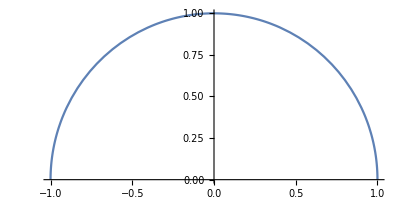

```mathematica
ParametricPlot[{Cos[t],Sin[t]},{t,0,Pi}]
```

### Parametric Plot of a Pendulum

Let’s look at sometime more interesting. Let’s use ParametricPlot to plot the trajectory of a pendulum.

In order to plot our pendulum, we are going to need a few variables. We start with our initial conditions.

```mathematica
theta0=Pi/3;
thetad0=0;
```

With these initial conditions, we are basically holding the pendulum at π/3, and at time zero, we just release it. 
Now we need some variables for gravity and length of pendulum’s rope.

```mathematica
g=9.81;
l=1;
wn=Sqrt[g/l];
```

Now let’s write out the equation that we saw.

```mathematica
theta=theta0 Cos[wn t]+1/wn thetad0 Sin[wn t]
```

0.+1/3 π Cos[3.13209 t]

Note here we haven’t defined t, but that’s ok. Mathematica will hold t for us for use later. I think it’s quite nice that when you evaluate equations like this in Mathematica, it converts some of the symbols for us, and simplifies the equation.

```mathematica
thetad=-wn theta0 Sin[wn t]+thetad0 Cos[wn t]
```

-3.27992 Sin[3.13209 t]

Now let’s plot these as functions of time. We will vary t from 0 to 10. We should also plot some legends. We should also label our x-axis.

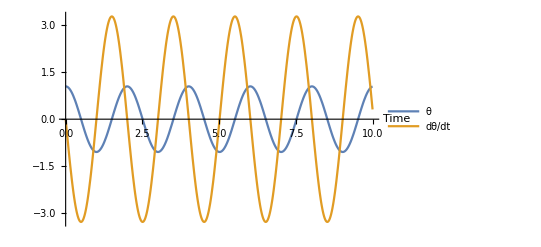

```mathematica
Plot[{theta,thetad},{t,0,10},PlotLegends->{"θ","dθ/dt"},AxesLabel->{"Time"}]
```

What we are looking at here, we have our blue curve, which is the position of the pendulum over time, and you can see it starts approximately π/2. The orange curve describe the velocity of the pendulum over time, and you can see it starts at 0. As the pendulum starts to fall, the velocity increases, until it reaches its maximum velocity, which is when pendulum is at it’s lowest point. Now the pendulum starts to go back up, and the velocity starts to decrease, until it reaches it’s slowest point, and then it continues again. As you can see it is periodic.

So it’s really great that we can see position and velocity over time. But what would be even neater is if we could trace the pendulum’s motion. We can do that with ParametricPlot.

We’ll just say:

Recall from trigonometry,  x = l sin(θ), y = - l cos(θ).

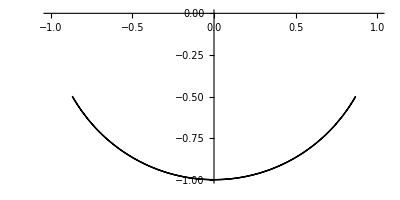

```mathematica
ParametricPlot[{l Sin[theta],-l Cos[theta]}, {t,0,1},PlotRange->{{-1,1},{-1,0}},PlotStyle->{Thick,Black}]
```

What we see here is a trace of our pendulum moving through space. This is only half a period. If we wanted to see it come back, we would have to plot it up to t=2.

```mathematica
ParametricPlot[{l Sin[theta],-l Cos[theta]}, {t,0,2},PlotRange->{{-1,1},{-1,0}},PlotStyle->{Thick,Black}]
```

-Graphics-

Now let’s take a look at the phase plot of our pendulum. The phase plot is basically the parametric plot of theta vs. thetadot.

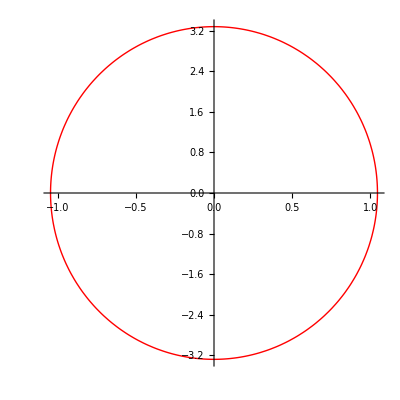

```mathematica
ParametricPlot[{theta,thetad},{t,0,2Pi/wn},PlotStyle->{Thick,Red},AspectRatio->1]
```

So phase plot allows us to see the state of the pendulum at a given time which is fully described by its displacement and velocity.

### Using ListLinePlot Parametrically

Let’s try something else. In a previous lecture we looked at Table function for generating data, and we used ListLinePlot to make some plots.

```mathematica
?Table
```

Table[expr,n] generates a list of n copies of expr. 
Table[expr,{i,i_max}] generates a list of the values of expr when i runs from 1 to i_max. 
Table[expr,{i,i_min,i_max}] starts with i=i_min. 
Table[expr,{i,i_min,i_max,di}] uses steps di. 
Table[expr,{i,{i_1,i_2,…}}] uses the successive values i_1, i_2, ….
Table[expr,{i,i_min,i_max},{j,j_min,j_max},…] gives a nested list. The list associated with i is outermost.

```mathematica
Table[{Cos[t],Sin[t]},{t,0,2Pi,0.1}]
```

{{1.,0.},{0.995004,0.0998334},{0.980067,0.198669},{0.955336,0.29552},{0.921061,0.389418},{0.877583,0.479426},{0.825336,0.564642},{0.764842,0.644218},{0.696707,0.717356},{0.62161,0.783327},{0.540302,0.841471},{0.453596,0.891207},{0.362358,0.932039},{0.267499,0.963558},{0.169967,0.98545},{0.0707372,0.997495},{-0.0291995,0.999574},{-0.128844,0.991665},{-0.227202,0.973848},{-0.32329,0.9463},{-0.416147,0.909297},{-0.504846,0.863209},{-0.588501,0.808496},{-0.666276,0.745705},{-0.737394,0.675463},{-0.801144,0.598472},{-0.856889,0.515501},{-0.904072,0.42738},{-0.942222,0.334988},{-0.970958,0.239249},{-0.989992,0.14112},{-0.999135,0.0415807},{-0.998295,-0.0583741},{-0.98748,-0.157746},{-0.966798,-0.255541},{-0.936457,-0.350783},{-0.896758,-0.44252},{-0.8481,-0.529836},{-0.790968,-0.611858},{-0.725932,-0.687766},{-0.653644,-0.756802},{-0.574824,-0.818277},{-0.490261,-0.871576},{-0.400799,-0.916166},{-0.307333,-0.951602},{-0.210796,-0.97753},{-0.112153,-0.993691},{-0.0123887,-0.999923},{0.087499,-0.996165},{0.186512,-0.982453},{0.283662,-0.958924},{0.377978,-0.925815},{0.468517,-0.883455},{0.554374,-0.832267},{0.634693,-0.772764},{0.70867,-0.70554},{0.775566,-0.631267},{0.834713,-0.550686},{0.88552,-0.464602},{0.927478,-0.373877},{0.96017,-0.279415},{0.983268,-0.182163},{0.996542,-0.0830894}}

```mathematica
?ListLinePlot
```

ListLinePlot[{y_1,y_2,…}] plots a line through a list of values, assumed to correspond to x coordinates 1, 2, … . 
ListLinePlot[{{x_1,y_1},{x_2,y_2},…}] plots a line through specific x and y positions. 
ListLinePlot[{list_1,list_2,…}] plots several lines.

Let’s use ListLinePlot and ParametricPlot in the same way, so we can see how to use ListLinePlot to plot parametric type data. So we need to start with some data that is parametrized, and we can use the Table function that we saw.

ListLinePlot requires pairwise data. So we use Table to generate pairwise data.

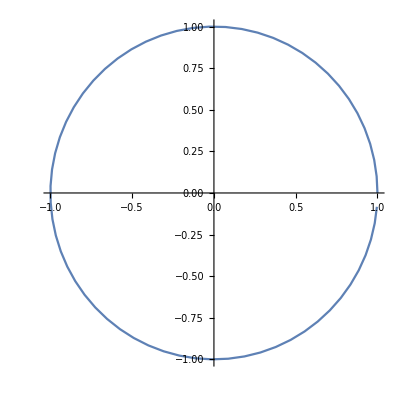

```mathematica
ListLinePlot[Table[{Cos[t],Sin[t]},{t,0,2Pi,0.1}],AspectRatio->1]
```

Now let’s take this ListLinePlot, and put it next to a ParametricPlot. Let’s use GraphicsRow, to plot these side by side.

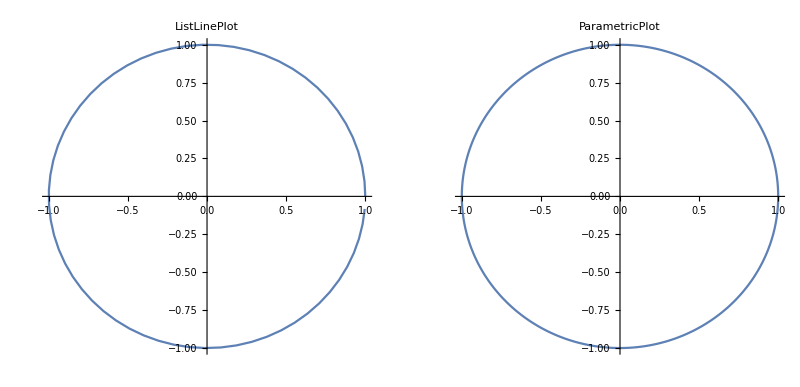

```mathematica
GraphicsRow[{ListLinePlot[Table[{Cos[t],Sin[t]},{t,0,2Pi,0.1}],AspectRatio->1,PlotLabel->"ListLinePlot"],
ParametricPlot[{Cos[t],Sin[t]},{t,0,2Pi},PlotLabel->"ParametricPlot"]}]
```

So here we have seen that ListLinePlot, and ParametricPlot can plot the same set of things.

### Parametric Plot of Lissajous Curve

Let’s try something even more cool. Let’s plot a Lissajous curve.

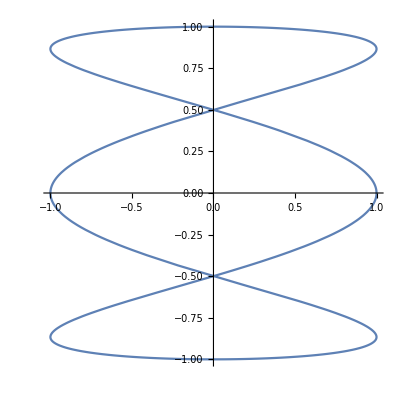

```mathematica
ParametricPlot[{Sin[3t+Pi/2],Sin[t]},{t,0,2Pi}]
```

There is out Lissajous curve. We can do this with ListLinePlot. We just need to use Table to generate our data.

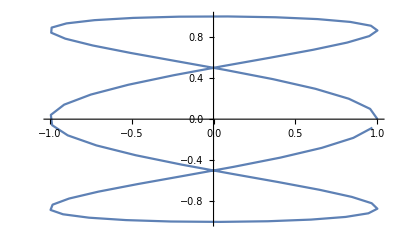

```mathematica
ListLinePlot[Table[{Sin[3t+Pi/2],Sin[t]},{t,0,2Pi,0.1}]]
```

Let’s put them in a GraphicsRow so we can compare them.

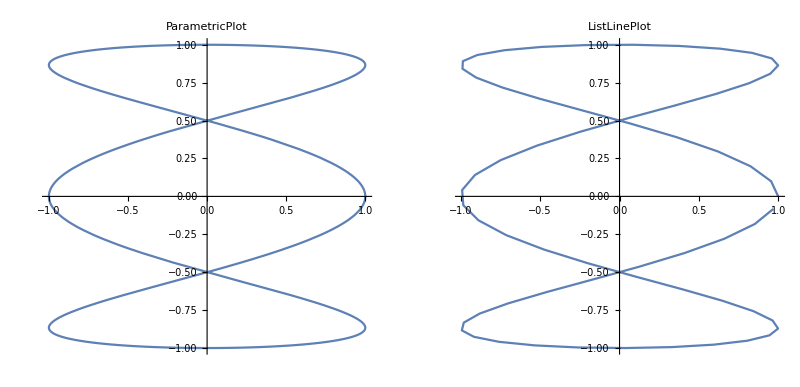

```mathematica
GraphicsRow[{ParametricPlot[{Sin[3t+Pi/2],Sin[t]},{t,0,2Pi},PlotLabel->"ParametricPlot",AspectRatio->1],
ListLinePlot[Table[{Sin[3t+Pi/2],Sin[t]},{t,0,2Pi,0.1}],PlotLabel->"ListLinePlot",AspectRatio->1]}]
```

There are our Lissajous curve.

### Summary

This concludes our lesson on ParametricPlot. We hope you had fun. I hope you go and try out some of these other initial conditions for the pendulum to see for your self what else this can do, and then I’ll see you in the next lecture.